Лабораторная работа №2
Численное решение задачи Коши для системы дифференциальных уравнений  методом Рунге-Кутты четвертого порядка

Метод Рунге-Кутты 4 порядка с шагом h:

```mathematica
f[t_,x1_,x2_]:=t^2*x1+x2;
g[t_,x1_,x2_]:=Cos[x1+t*x2];
h=0.1;
a=0;
b=2;
n=(b-a)/h;
t=a;
x1=-1;
x2=1;
tx1={{t,x1}};
tx2={{t,x2}};
tx1x2={{t,x1,x2}};
For[i=0,i<n,i++,
m1=h*f[t,x1,x2];
k1=h*g[t,x1,x2];
m2=h*f[t+h/2,x1+m1/2,x2+k1/2];
k2=h*g[t+h/2,x1+m1/2,x2+k1/2];
m3=h*f[t+h/2,x1+m2/2,x2+k2/2];
k3=h*g[t+h/2,x1+m2/2,x2+k2/2];
m4=h*f[t+h,x1+m3,x2+k3];
k4=h*g[t+h,x1+m3,x2+k3];
x1=x1+(m1+2m2+2m3+m4)/6;
x2=x2+(k1+2k2+2k3+k4)/6;
t=t+h;
tx1x2=Append[tx1x2,{t,x1,x2}];
tx1=Append[tx1,{t,x1}];
tx2=Append[tx2,{t,x2}]];
s=Table[{tx1x2[[j,1]],tx1x2[[j,2]],tx1x2[[j,3]]},{j,21}];
Grid[Join[{{"t","x1, шаг h","x2, шаг h"}},s],Frame->All]
```

t | x1, шаг h | x2, шаг h
0 | -1 | 1
0.1 | -0.89733 | 1.06227
0.2 | -0.789279 | 1.13998
0.3 | -0.675444 | 1.23037
0.4 | -0.555057 | 1.32865
0.5 | -0.427123 | 1.42742
0.6 | -0.290565 | 1.51698
0.7 | -0.144251 | 1.58684
0.8 | 0.0132162 | 1.62826
0.9 | 0.184024 | 1.63655
1. | 0.371966 | 1.61184
1.1 | 0.583501 | 1.55804
1.2 | 0.829113 | 1.48122
1.3 | 1.12529 | 1.38859
1.4 | 1.49774 | 1.28921
1.5 | 1.98706 | 1.19756
1.6 | 2.65902 | 1.14198
1.7 | 3.62343 | 1.16885
1.8 | 5.06438 | 1.25603
1.9 | 7.28104 | 1.21493
2. | 10.7967 | 1.21994

Метод Рунге - Кутты 4 порядка с шагом h/2 :

```mathematica
f[t_,x1_,x2_]:=t^2*x1+x2;
g[t_,x1_,x2_]:=Cos[x1+t*x2];
```

```mathematica
h2=h/2;
n=(b-a)/h2;
t1=a;
x1=-1;
x2=1;
t1x1={{t1,x1}};
t1x2={{t1,x2}};
t1x1x2={{t1,x1,x2}};
For[i=0,i<n,i++,
m1=h2*f[t1,x1,x2];
k1=h2*g[t1,x1,x2];
m2=h2*f[t1+h2/2,x1+m1/2,x2+k1/2];
k2=h2*g[t1+h2/2,x1+m1/2,x2+k1/2];
m3=h2*f[t1+h2/2,x1+m2/2,x2+k2/2];
k3=h2*g[t1+h2/2,x1+m2/2,x2+k2/2];
m4=h2*f[t1+h2,x1+m3,x2+k3];
k4=h2*g[t1+h2,x1+m3,x2+k3];
x1=x1+(m1+2m2+2m3+m4)/6;
x2=x2+(k1+2k2+2k3+k4)/6;
t1=t1+h2;
t1x1x2=Append[t1x1x2,{t1,x1,x2}];
t1x1=Append[t1x1,{t1,x1}];
t1x2=Append[t1x2,{t1,x2}]];
```

```mathematica
s=Table[{t1x1x2[[j,1]],t1x1x2[[j,2]],t1x1x2[[j,3]]},{j,41}];
Grid[Join[{{"t","x1, шаг h/2","x2, шаг h/2"}},s],Frame->All]
```

t | x1, шаг h/2 | x2, шаг h/2
0 | -1 | 1
0.05 | -0.94933 | 1.0291
0.1 | -0.89733 | 1.06227
0.15 | -0.843992 | 1.09933
0.2 | -0.789279 | 1.13998
0.25 | -0.733126 | 1.18383
0.3 | -0.675445 | 1.23038
0.35 | -0.616129 | 1.27893
0.4 | -0.555057 | 1.32865
0.45 | -0.4921 | 1.37854
0.5 | -0.427124 | 1.42742
0.55 | -0.359991 | 1.47401
0.6 | -0.290566 | 1.51698
0.65 | -0.218704 | 1.555
0.7 | -0.144251 | 1.58684
0.75 | -0.0670203 | 1.61151
0.8 | 0.0132181 | 1.62826
0.85 | 0.0967668 | 1.63664
0.9 | 0.184027 | 1.63655
0.95 | 0.27553 | 1.62814
1. | 0.371971 | 1.61184
1.05 | 0.474248 | 1.58823
1.1 | 0.583507 | 1.55804
1.15 | 0.701194 | 1.52208
1.2 | 0.829121 | 1.48121
1.25 | 0.969548 | 1.43638
1.3 | 1.1253 | 1.38858
1.35 | 1.29989 | 1.33903
1.4 | 1.49775 | 1.28921
1.45 | 1.72445 | 1.2411
1.5 | 1.98708 | 1.19755
1.55 | 2.29472 | 1.16261
1.6 | 2.65908 | 1.14198
1.65 | 3.09541 | 1.14251
1.7 | 3.62355 | 1.16907
1.75 | 4.26913 | 1.21571
1.8 | 5.06463 | 1.25638
1.85 | 6.05105 | 1.25702
1.9 | 7.28175 | 1.21491
1.95 | 8.82987 | 1.1868
2. | 10.7979 | 1.2244

Графики x1(t),x2(t):

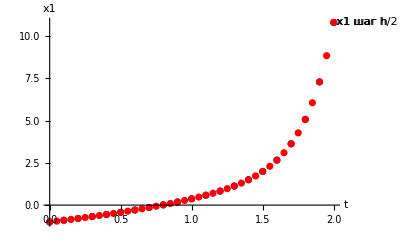

```mathematica
Show[ListPlot[Labeled[tx1,"x1 шаг h"],PlotStyle->Blue],ListPlot[Labeled[t1x1,"x1 шаг h/2"],PlotStyle->Red],AxesLabel->{HoldForm[t],HoldForm[x1]}]
```

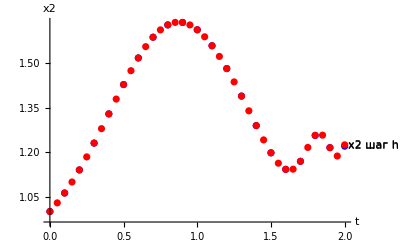

```mathematica
Show[ListPlot[Labeled[tx2,"x2 шаг h"],PlotStyle->Blue],ListPlot[Labeled[t1x2,"x2 шаг h"],PlotStyle->Red],AxesLabel->{HoldForm[t],HoldForm[x2]}]
```

Графики фазовых траекторий:

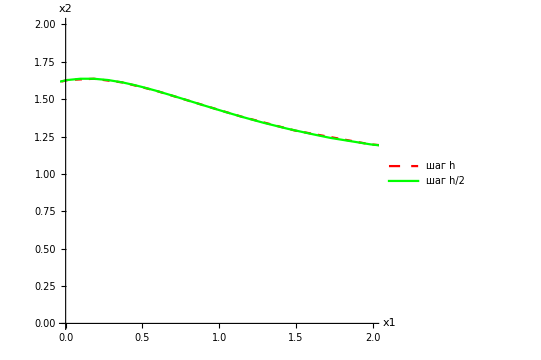

```mathematica
{sol1,sol2}={Interpolation[tx1,InterpolationOrder->1],Interpolation[tx2,InterpolationOrder->1]};
{sol11,sol22}={Interpolation[t1x1,InterpolationOrder->1],Interpolation[t1x2,InterpolationOrder->1]};
Show[ParametricPlot[{sol1[t],sol2[t]},{t,0,2},AxesLabel->{"x1","x2"},PlotRange->{0,2},PlotStyle->{Red,Dashed},PlotLegends->{Placed[{Text[Style["шаг h",12]]},{0.6,0.9}]},AspectRatio->0.9],ParametricPlot[{sol11[t],sol22[t]},{t,0,2},AxesLabel->{"x1","x2"},PlotRange->{0,2},PlotStyle->Green,PlotLegends->{Placed[{Text[Style["шаг h/2",12]]},{0.7,0.7}]},AspectRatio->0.9]]
```

Метод Рунге - Кутты 4 порядка с шагом 2h :

```mathematica
h3=2*h;
n3=(b-a)/h3;
t2=a;
x1=-1;
x2=1;
t2x1={{t2,x1}};
t2x2={{t2,x2}};
t2x1x2={{t2,x1,x2}};
For[i=0,i<n3,i++,
m1=h3*f[t2,x1,x2];
k1=h3*g[t2,x1,x2];
m2=h3*f[t2+h3/2,x1+m1/2,x2+k1/2];
k2=h3*g[t2+h3/2,x1+m1/2,x2+k1/2];
m3=h3*f[t2+h3/2,x1+m2/2,x2+k2/2];
k3=h3*g[t2+h3/2,x1+m2/2,x2+k2/2];
m4=h3*f[t2+h3,x1+m3,x2+k3];
k4=h3*g[t2+h3,x1+m3,x2+k3];
x1=x1+(m1+2m2+2m3+m4)/6;
x2=x2+(k1+2k2+2k3+k4)/6;
t2=t2+h3;
t2x1x2=Append[t2x1x2,{t2,x1,x2}];
t2x1=Append[t2x1,{t2,x1}];
t2x2=Append[t2x2,{t2,x2}]];
```

Погрешность между  h/2:

```mathematica
pogr1={};
pogr2={};
Pogresh1=0;
PogreshTest=0;
For[i=1,i<=n3+1,i++,
t3x1=1/15*Abs[t1x1[[2i-1,2]]-tx1[[i,2]]];
t3x2=1/15*Abs[t1x2[[2i-1,2]]-tx2[[i,2]]];
PogreshTest=Sqrt[t3x1^2+t3x2^2];
If[PogreshTest>Pogresh1,Pogresh1=PogreshTest]];
Pogresh1
```

3.34689×10^-7

```mathematica
Погрешность между h и2h:
```

```mathematica
Pogresh2=0;
PogreshTest=0;
For[i=1,i<=n3+1,i++,
t3x1=1/15*Abs[tx1[[2i-1,2]]-t2x1[[i,2]]];
t3x2=1/15*Abs[tx2[[2i-1,2]]-t2x2[[i,2]]];
PogreshTest=Sqrt[t3x1^2+t3x2^2];
If[PogreshTest>Pogresh2,Pogresh2=PogreshTest]];
Pogresh2
```

0.00373008